```mathematica
<< Toolbox`Style`
<< Toolbox`
<< XML`
SetDirectory[NotebookDirectory[]];
SetDirectory[".."];
<< util`
```

# SB2 Systems Biology : Simulation of Dynamic Network States

## Glycolysis

### Construct model

```mathematica
chemicalFormulas={glu^c->"C6H12O6",g6p^c->"H11C6O9P",f6p^c->"H11C6O9P",fdp^c->"H10C6O12P2",dhap^c->"H5C3O6P",gap^c->"H5C3O6P",pg13^c->"H4C3O10P2",pg3^c->"H4C3O7P",pg2^c->"H4C3O7P",pep^c->"H2C3O6P",pyr^c->"H3C3O3",lac^c->"H5C3O3",nad^c->"&NAD&",nadh^c->"H&NAD&",amp^c->"H13C10N5O7P",adp^c->"H13C10N5O10P2",atp^c->"H13C10N5O13P3",phos^c->"HO4P",h^c->"H",h2o^c->"H2O"};
rxns={Overscript[atp^c+glu^c⇌adp^c+g6p^c+h^c, vhk],Overscript[g6p^c⇌f6p^c, vpgi],Overscript[atp^c+f6p^c⇌adp^c+fdp^c+h^c, vpfk],Overscript[dhap^c⇌gap^c, vtpi],Overscript[fdp^c⇌dhap^c+gap^c, vald],Overscript[gap^c+nad^c+phos^c⇌h^c+nadh^c+pg13^c, vgapdh],Overscript[adp^c+pg13^c⇌atp^c+pg3^c, vpgk],Overscript[pg3^c⇌pg2^c, vpglm],Overscript[pg2^c⇌h2o^c+pep^c, veno],Overscript[adp^c+h^c+pep^c⇌atp^c+pyr^c, vpk],Overscript[h^c+nadh^c+pyr^c⇌lac^c+nad^c, vldh],(amp^c⇌∅)^vamp,Overscript[2 adp^c⇌amp^c+atp^c, vapk],(pyr^c⇌∅)^vpyr,(lac^c⇌∅)^vlac,Overscript[atp^c+h2o^c⇌adp^c+h^c+phos^c, vatp],Overscript[nadh^c⇌h^c+nad^c, vnadh],(∅⇌glu^c)^vgluin,(∅⇌amp^c)^vampin,(h^c⇌∅)^vh,(h2o^c⇌∅)^vh2o};
equilibriumConstants={Underscript[K, vhk]->850,Underscript[K, vpgi]->0.41,Underscript[K, vpfk]->310,Underscript[K, vtpi]->0.05714285714285714,Underscript[K, vald]->0.082 Millimole Liter^-1,Underscript[K, vgapdh]->0.0179 Liter Millimole^-1,Underscript[K, vpgk]->1800,Underscript[K, vpglm]->0.14705882352941177,Underscript[K, veno]->1.6949152542372883,Underscript[K, vpk]->363000,Underscript[K, vldh]->26300,Underscript[K, vamp]->∞,Underscript[K, vapk]->1.65,Underscript[K, vpyr]->1.,Underscript[K, vlac]->1.,Underscript[K, vatp]->∞ Millimole Liter^-1,Underscript[K, vnadh]->∞,Underscript[K, vgluin]->∞,Underscript[K, vampin]->∞,Underscript[K, vh]->1.,Underscript[K, vh2o]->1.};
externalFixedConc={pyr^Xt->0.06 Millimole Liter^-1,amp^Xt->Millimole Liter^-1,h^Xt->0.00006309573444801929 Millimole Liter^-1,metabolite[_,"Xt"]->Millimole Liter^-1};
steadyStateConcentrations={glu^c->1. Millimole Liter^-1,g6p^c->0.0486 Millimole Liter^-1,f6p^c->0.0198 Millimole Liter^-1,fdp^c->0.0146 Millimole Liter^-1,dhap^c->0.16 Millimole Liter^-1,gap^c->0.00728 Millimole Liter^-1,pg13^c->0.000243 Millimole Liter^-1,pg3^c->0.0773 Millimole Liter^-1,pg2^c->0.0113 Millimole Liter^-1,pep^c->0.017 Millimole Liter^-1,pyr^c->0.060301 Millimole Liter^-1,lac^c->1.36 Millimole Liter^-1,nad^c->0.0589 Millimole Liter^-1,nadh^c->0.0301 Millimole Liter^-1,amp^c->0.08672812499999999 Millimole Liter^-1,adp^c->0.29 Millimole Liter^-1,atp^c->1.6 Millimole Liter^-1,phos^c->2.5 Millimole Liter^-1,h^c->0.00008997573444801929 Millimole Liter^-1,h2o^c->1. Millimole Liter^-1};
glycolysis=constructModel[rxns,
ElementalComposition->chemicalFormulas,
Ignore->{m["h","c"],m["h2o","c"]},
InitialConditions->steadyStateConcentrations,
Parameters->Join[equilibriumConstants,externalFixedConc],
Notes->defaultInitializationNotes[],
UnitChecking->True
];

null=({
 {1, 0, 1},
 {1, 0, 0},
 {0, 1, 0}
}).NullSpace[glycolysis];
gluin=1.12;
ststloadnadh=0.2*gluin;
ampin=.014;
givenststfluxes=({
 {gluin, ststloadnadh, ampin}
});
solution=Flatten[Transpose[givenststfluxes.null]];
steadyStateFluxes=#[[1]]->#[[2]]Millimole Liter^-1 Hour^-1&/@Thread[Rule[glycolysis["Fluxes"],solution]];

updateInitialConditions[glycolysis,steadyStateFluxes];

perc=calcPERC[glycolysis]/.Undefined->100000;
updateParameters[glycolysis,perc];

SetDirectory[NotebookDirectory[]];
Export["../../models/SB2/glycolysis.m.gz",glycolysis]
```

calcPERC::atequilibrium: Reaction "vapk" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to Undefined (this value can be specified using the option "AtEquilibriumDefault").

calcPERC::atequilibrium: Reaction "vh2o" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to Undefined (this value can be specified using the option "AtEquilibriumDefault").

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed.

../../models/SB2/glycolysis.m.gz

### Analyze model

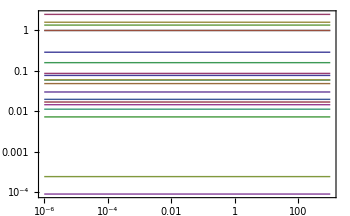

```mathematica
{concSol,fluxSol}=simulate[glycolysis,{t,0,1000}];
plotSimulation[concSol,{t,0,1000}]
```

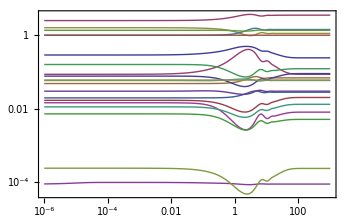

```mathematica
{concSol,fluxSol}=simulate[glycolysis,{t,0,1000},Parameters->{rateconst["vatp", True]->2 Hour^-1}];
plotSimulation[concSol,{t,0,1000}]
```

```mathematica
TraditionalForm@TableForm[glycolysis["InitialConditions"]]
```

glu^c→1. mmol l^-1
g6p^c→0.0486 mmol l^-1
f6p^c→0.0198 mmol l^-1
fdp^c→0.0146 mmol l^-1
dhap^c→0.16 mmol l^-1
gap^c→0.00728 mmol l^-1
pg13^c→0.000243 mmol l^-1
pg3^c→0.0773 mmol l^-1
pg2^c→0.0113 mmol l^-1
pep^c→0.017 mmol l^-1
pyr^c→0.060301 mmol l^-1
lac^c→1.36 mmol l^-1
nad^c→0.0589 mmol l^-1
nadh^c→0.0301 mmol l^-1
amp^c→0.0867281 mmol l^-1
adp^c→0.29 mmol l^-1
atp^c→1.6 mmol l^-1
phos^c→2.5 mmol l^-1
h^c→0.0000899757 mmol l^-1
h2o^c→1. mmol l^-1
v_vhk→1.12 mmol h^-1 l^-1
v_vpgi→1.12 mmol h^-1 l^-1
v_vpfk→1.12 mmol h^-1 l^-1
v_vtpi→1.12 mmol h^-1 l^-1
v_vald→1.12 mmol h^-1 l^-1
v_vgapdh→2.24 mmol h^-1 l^-1
v_vpgk→2.24 mmol h^-1 l^-1
v_vpglm→2.24 mmol h^-1 l^-1
v_veno→2.24 mmol h^-1 l^-1
v_vpk→2.24 mmol h^-1 l^-1
v_vldh→2.016 mmol h^-1 l^-1
v_vamp→0.014 mmol h^-1 l^-1
v_vapk→0. mmol h^-1 l^-1
v_vpyr→0.224 mmol h^-1 l^-1
v_vlac→2.016 mmol h^-1 l^-1
v_vatp→2.24 mmol h^-1 l^-1
v_vnadh→0.224 mmol h^-1 l^-1
v_vgluin→1.12 mmol h^-1 l^-1
v_vampin→0.014 mmol h^-1 l^-1
v_vh→2.688 mmol h^-1 l^-1
v_vh2o→0. mmol h^-1 l^-1

```mathematica
TraditionalForm@TableForm[stripUnits@glycolysis["Parameters"]]
```

Volume_c→1
K_vhk→850
K_vpgi→0.41
K_vpfk→310
K_vtpi→0.0571429
K_vald→0.082
K_vgapdh→0.0179
K_vpgk→1800
K_vpglm→0.147059
K_veno→1.69492
K_vpk→363000
K_vldh→26300
K_vamp→∞
K_vapk→1.65
K_vpyr→1.
K_vlac→1.
K_vatp→∞
K_vnadh→∞
K_vgluin→∞
K_vampin→∞
K_vh→1.
K_vh2o→1.
pyr^Xt→0.06
amp^Xt→1
h^Xt→0.0000630957
k_vhk^⟶→0.700007
k_vpgi^⟶→3644.44
k_vpfk^⟶→35.3688
k_vtpi^⟶→34.3558
k_vald^⟶→2834.57
k_vgapdh^⟶→3376.75
k_vpgk^⟶→1.27353×10^6
k_vpglm^⟶→4869.57
k_veno^⟶→1763.78
k_vpk^⟶→454.386
k_vldh^⟶→1112.57
k_vamp^⟶→0.161424
k_vapk^⟶→100000
k_vpyr^⟶→744.186
k_vlac^⟶→5.6
k_vatp^⟶→1.4
k_vnadh^⟶→7.44186
k_vgluin^⟶→1.12
k_vampin^⟶→0.014
k_vh^⟶→100000.
k_vh2o^⟶→100000
metabolite(_,Xt)→1

```mathematica
plotPhasePortrait[concSol/.m_metabolite:>ToString[m]]
```